## Evolution of indirect reciprocity by image scoring

Assumptions
1. Random pairs of players are chosen, of which one is the potential donor of some altruistic act and the other is the recipient. The donor can cooperate and help the recipient at a cost c to himself, in which case the recipient receives a benefit of value b (with b > c).If the donor decides not to help, both individuals receive zero pay - off.
   
2. Each player has an image score, s, which is known to every other player. If a player is chosen as a donor and decides to cooperate, then his (or her) image score increases by one unit; if the donor does not cooperate then it decreases by one unit.The image score of a recipient does not change.
   
3. We consider strategies where donors decide to help according to the image score of the recipient.A strategy is given by a number k : a player with this strategy provides help if, and only if, the image score of the potential recipient is at least k. the strategy (k) values from -5 to +6. The strategy k=-5 represents unconditional cooperators, whereas the strategy k=6 represents defectors
The strategies are given by ki and the image levels by si. A donor, i, cooperates with a recipient, j, if ki <= sj. At the beginning of each generation, the image levels of all players are zero.
   
4. In succession, m donor - recipient pairs are chosen. The fitness of a player is given by the total number of points received during the m interactions.Some players may never be chosen, in which case their payoff from the game will be zero. On average, a player will be chosen 2 m/n times, either as donor or as recipient.
   
5. At the end of each generation, players leave offspring in proportion to their fitness.

```mathematica
戦略別に適合度を計算して，各個体にルーレットセレクションを実行する
```

```mathematica
image[n_(*集団人数*),m_(*ペア個数*),gene_(*世代*)]:=Module[
{b=1,c=0.1,id(*n人分の個体番号*),klist(*　n人分の戦略*),slist(*n人分のimage score*),
benefit(*n人分の利得*),pair(*m組の番号対*),fit(*k個の適合度*)},

(*初期条件の入力 *)
id=Range[n];(* マッチング用個体番号 *)
slist=Table[0,{n}];(*イメージスコア初期値 Print[slist];*)
klist=Table[Random[Integer,{-5,6}],{n}];(*　戦略kの初期値　Print["klist初期値=",klist];*)
benefit=Table[0,{n}];(*利得の初期値態 *)

Do[(* ここから1世代内での行動を指定する *)
(*最初にイメージスコアslist，利得benefit，適合度fitを初期化する*)
slist=Table[0,{n}];(* slist初期化 *)
benefit=Table[0,{n}];(* 利得benefit初期化 *)
fit=Table[0,{12}];(*戦略別適合度fitの初期化*)

Do[(*「pairを一個だけ作る操作」をDoでm回反復してm個のペアを作る．
slistはペアを1個作るたびに即時更新される．slistは1世代内(gene内)でも更新される *)
pair=RandomSample[id,2];(*　ペアを一つ作る　*)

If[klist⟦pair⟦1⟧⟧<=slist⟦pair⟦2⟧⟧,(* 相手のイメージスコアをチェック *)
benefit⟦pair⟦2⟧⟧=benefit⟦pair⟦2⟧⟧+b;benefit⟦pair⟦1⟧⟧=benefit⟦pair⟦1⟧⟧-c;
If[slist⟦pair⟦1⟧⟧≤5,slist⟦pair⟦1⟧⟧=slist⟦pair⟦1⟧⟧+1,slist⟦pair⟦1⟧⟧=5],(* ここまで協力時の行動*)
If[slist⟦pair⟦1⟧⟧≥-5,slist⟦pair⟦1⟧⟧=slist⟦pair⟦1⟧⟧-1,slist⟦pair⟦1⟧⟧=-5]
(* image scoreのレンジを[-5,5]に制限する事で無条件の協力・裏切りを定義する*)];
benefit=benefit+c(* benefitの非零化.RandomChoiceの重み用*),{m}];(*m個のマッチング反復終わり*)
(*戦略別に利得を合計して適合度fitに代入*)
Table[Table[If[klist⟦i⟧==(j-6),fit⟦j⟧=fit⟦j⟧+benefit⟦i⟧],{j,1,12}],{i,1,n}];
(*  適合度に基づくルーレットセレクション　*)
klist=Table[RandomChoice[(*weight*)fit->{-5,-4,-3,-2,-1,0,1,2,3,4,5,6}],{i,1,n}],{gene}];
(*世代geneの反復Do おわり*)
Print[Table[Count[klist,i-6],{i,1,12}]];(* 最終的な戦略kの分布 *)
ListPlot[Table[{i-6,Count[klist,i-6]},{i,1,12}],PlotRange->{0,110},
Filling->Axis,PlotStyle->PointSize[Large]]
(* 戦略分布の可視化 *)]
```

{0,7,34,0,0,87,0,0,0,72,0,0}

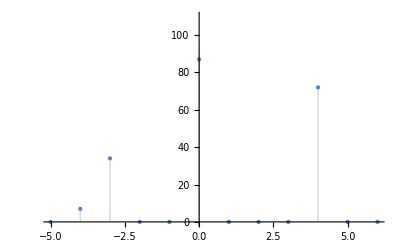

```mathematica
image[200(*集団人数*),150(*ペア個数*),200(*世代*)]
```

## 計算

```mathematica
image[100(*集団人数*),150(*ペア個数*),200(*世代*)]
```

## コードの実験

```mathematica
Module[{klist,n=10,benefit,fit},
klist=Table[Random[Integer,{-5,6}],{n}];
benefit=Table[Random[Integer,{0,10}],{n}];
Print[klist];
Print[benefit];
fit=Table[0,{12}];(*戦略別適合度*)
Table[
Table[
If[klist⟦i⟧==(j-6),fit⟦j⟧=fit⟦j⟧+benefit⟦i⟧],{j,1,12}],{i,1,n}];
fit]
```

{1,2,-3,-2,2,0,4,-2,4,2}

{9,3,4,5,3,3,3,7,0,3}

{0,0,4,12,0,3,9,9,0,3,0,0}

```mathematica
n=Range[100]
```

```mathematica
{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}
```

```mathematica
Module[{x={1,1}},
While[x[[1]]==x[[2]];
x=RandomInteger[{1,100},2]];
x]
```

{55,48}

```mathematica
x1=RandomInteger[{1,100}];
```

```mathematica
RandomSample[Range[10],2]
```

{10,4}

```mathematica
image2[n_(*集団人数*),m_(*ペア個数*),gene_(*世代*)]:=Module[
{b=1,c=0.1,id(*n人分の個体番号*),klist(*　n人分の戦略*),slist(*n人分のimage score*),
benefit(*n人分の利得*),pair(*m組の番号対*),fit(*k個の適合度*)},

(*初期条件の入力 *)
id=Range[n];(* マッチング用個体番号 *)
slist=Table[0,{n}];(*イメージスコア初期値 Print[slist];*)
klist=Table[Random[Integer,{-5,6}],{n}];(*　戦略kの初期値　Print["klist初期値=",klist];*)
benefit=Table[0,{n}];(*利得の初期値態 *)

Do[(* ここから1世代内での行動を指定する *)
(*最初にイメージスコアslist，利得benefit，適合度fitを初期化する*)
slist=Table[0,{n}];(* slist初期化 *)
benefit=Table[0,{n}];(* 利得benefit初期化 *)
fit=Table[0,{12}];(*戦略別適合度fitの初期化*)

Do[(*「pairを一個だけ作る操作」をDoでm回反復してm個のペアを作る．
slistはペアを1個作るたびに即時更新される．slistは1世代内(gene内)でも更新される *)
pair=RandomSample[id,2];(*　ペアを一つ作る　*)

If[klist⟦pair⟦1⟧⟧<=slist⟦pair⟦2⟧⟧,(* 相手のイメージスコアをチェック *)
benefit⟦pair⟦2⟧⟧=benefit⟦pair⟦2⟧⟧+b;benefit⟦pair⟦1⟧⟧=benefit⟦pair⟦1⟧⟧-c;
If[slist⟦pair⟦1⟧⟧≤5,slist⟦pair⟦1⟧⟧=slist⟦pair⟦1⟧⟧+1,slist⟦pair⟦1⟧⟧=5],(* ここまで協力時の行動*)
If[slist⟦pair⟦1⟧⟧≥-5,slist⟦pair⟦1⟧⟧=slist⟦pair⟦1⟧⟧-1,slist⟦pair⟦1⟧⟧=-5]
(* image scoreのレンジを[-5,5]に制限する事で無条件の協力・裏切りを定義する*)];
benefit=benefit+c(* benefitの非零化.RandomChoiceの重み用*),{m}];(*m個のマッチング反復終わり*)
(*戦略別に利得を合計して適合度fitに代入*)
Table[Table[If[klist⟦i⟧==(j-6),fit⟦j⟧=fit⟦j⟧+benefit⟦i⟧],{j,1,12}],{i,1,n}];
(*  適合度に基づくルーレットセレクション　*)
klist=Table[RandomChoice[(*weight*)fit->{-5,-4,-3,-2,-1,0,1,2,3,4,5,6}],{i,1,n}];
Print[ListPlot[Table[{i-6,Count[klist,i-6]},{i,1,12}],PlotRange->{0,110},
Filling->Axis,PlotStyle->PointSize[Large]]]
,{gene}];
(*世代geneの反復Do おわり*)
Print[Table[Count[klist,i-6],{i,1,12}]];(* 最終的な戦略kの分布 *)
ListPlot[Table[{i-6,Count[klist,i-6]},{i,1,12}],PlotRange->{0,110},
Filling->Axis,PlotStyle->PointSize[Large]]
(* 戦略分布の可視化 *)]
```

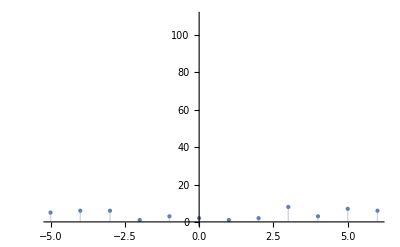

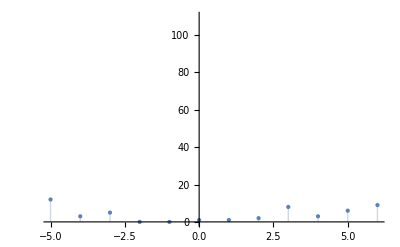

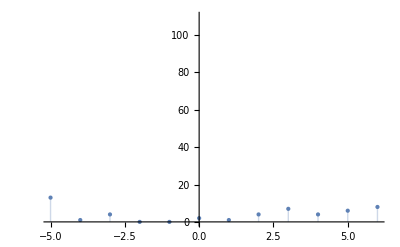

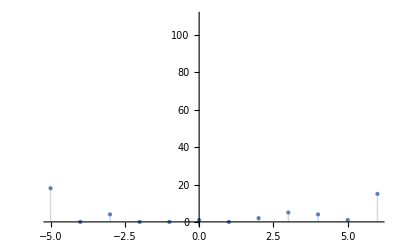

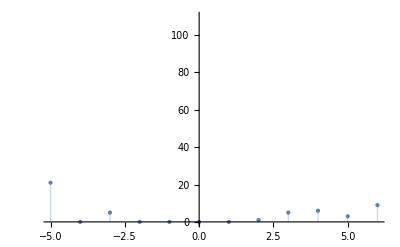

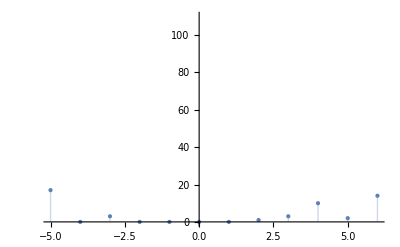

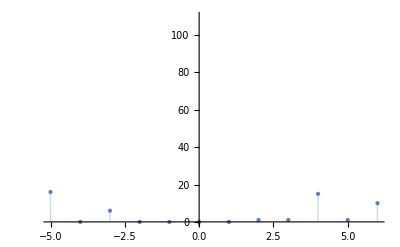

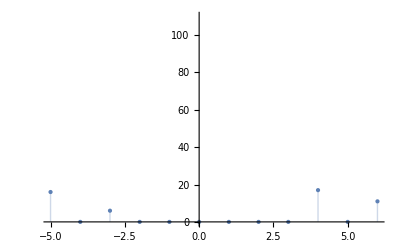

-Graphics-

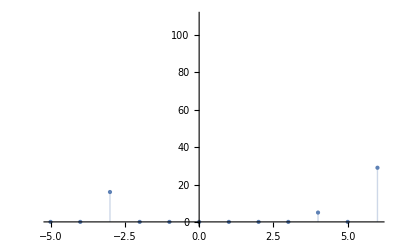

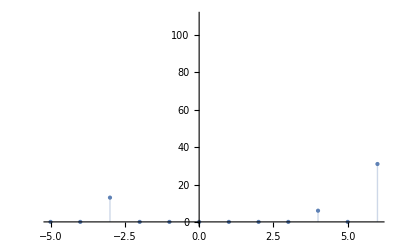

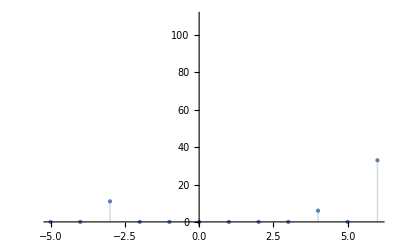

-Graphics-

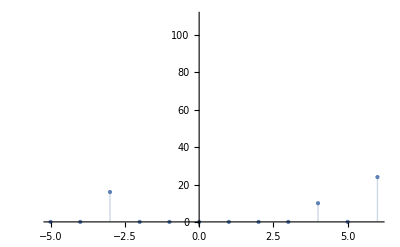

-Graphics-

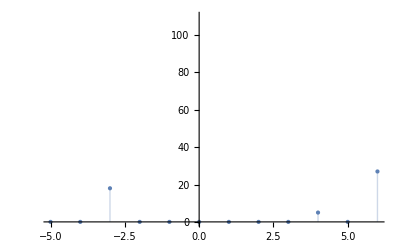

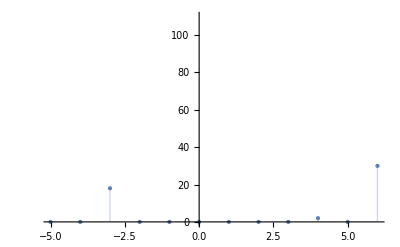

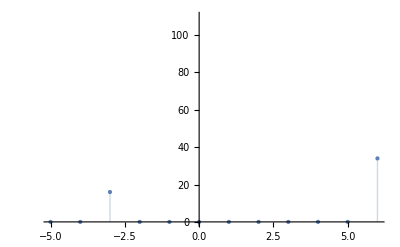

-Graphics-

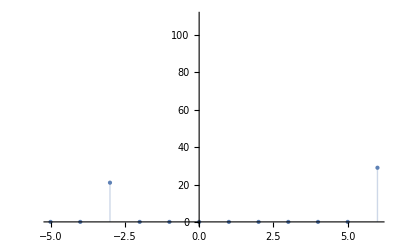

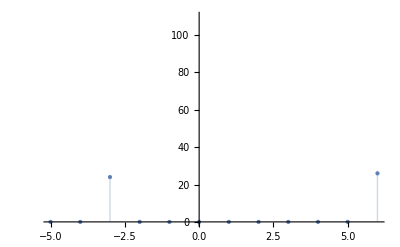

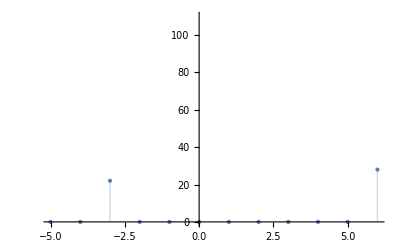

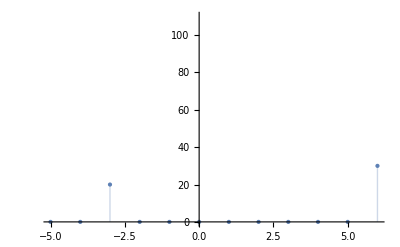

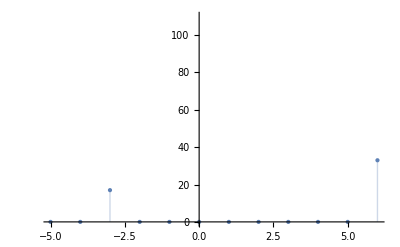

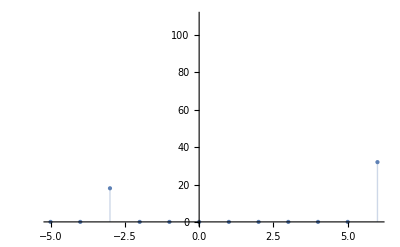

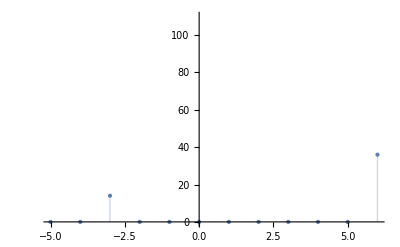

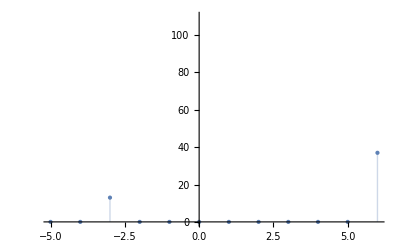

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

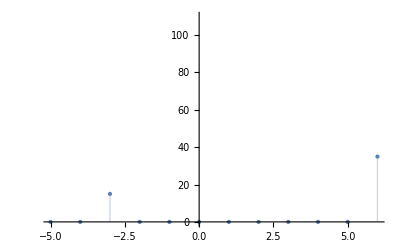

-Graphics-

-Graphics-

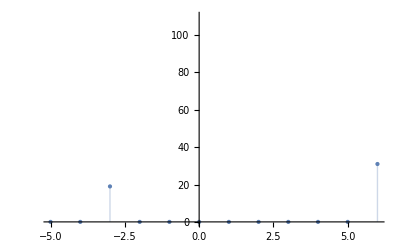

-Graphics-

-Graphics-

-Graphics-

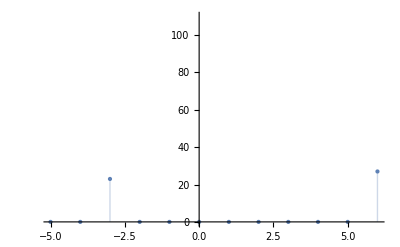

-Graphics-

-Graphics-

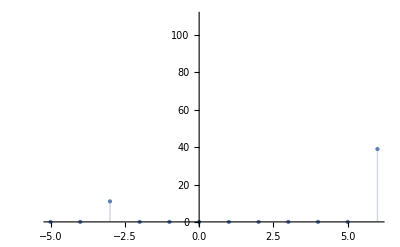

-Graphics-

-Graphics-

-Graphics-

-Graphics-

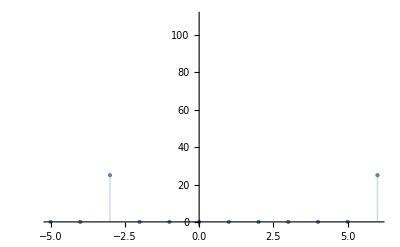

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

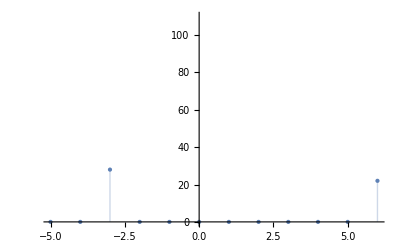

-Graphics-

-Graphics-

-Graphics-

-Graphics-

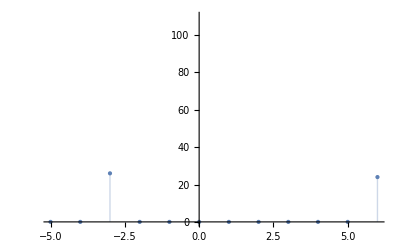

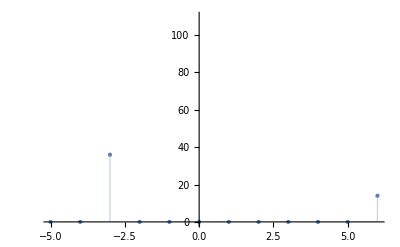

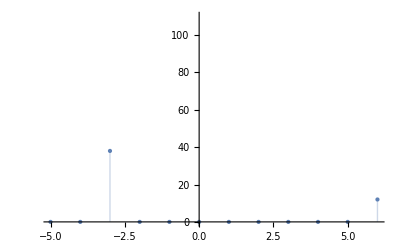

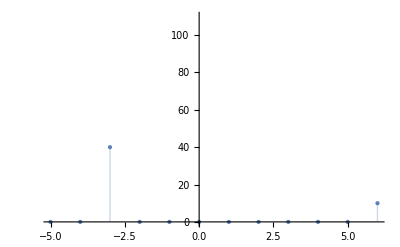

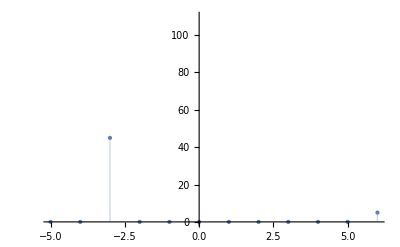

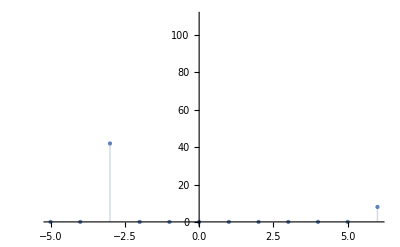

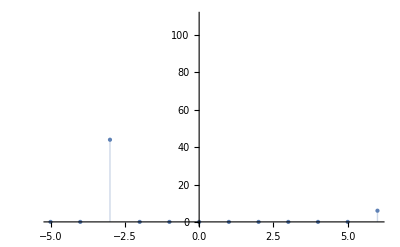

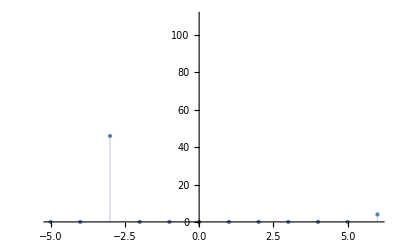

{0,0,49,0,0,0,0,0,0,0,0,1}

-Graphics-

```mathematica
image2[50(*集団人数*),100(*ペア個数*),100(*世代*)]
```